```mathematica
(* Figure 3 in the paper, demonstrates that the range of angles alpha in Area 3 is contained in [0.15, 0.24] *)
RegionPlot[{y ≤ Sqrt[x(1-x)] && 0.156 <=y <= 1.7x - 1.38, (y ≤ Sqrt[x(1-x)] && y ≥ x*Tan[0.15] && y ≤ x * Tan[0.24])}, {x, 0.7, 1}, {y, 0.14, 0.24}, PlotPoints -> 200, AspectRatio -> 3/5]
```

-Graphics-

```mathematica
F[q_] = 3 Pi^2(1+(4q^2)^(1/3))^3/q
```

(3 π^2 (1+2^(2/3) (q^2)^(1/3))^3)/q

```mathematica
G[a_] = 7 a BesselJZero[Pi/a, 1]^2
```

7 a BesselJZero[π/a,1]^2

```mathematica
(* Calculations supporting the proof that g is decreasing in our region of interest *)
j0 = BesselJZero[0, 1] // N
j13 = BesselJZero[13, 1] // N
diff = j13 - BesselJZero[12, 1] // N
```

2.40483

17.8014

1.10319

```mathematica
(* Checking the validity of pairs (q0, alpha0) *)
F[0.15]/G[0.2]
F[0.185]/G[0.225]
F[0.21]/G[0.24]
```

0.992858

0.994264

0.995939

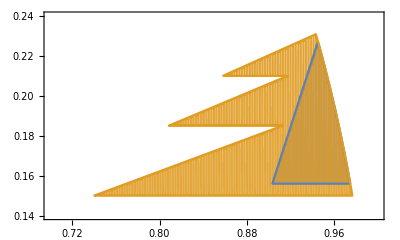

```mathematica
(* Figure 4 in the paper, demonstrates that the regions S_{q0, a0} cover area III *)
RegionPlot[{y ≤ Sqrt[1/4 - (x - 1/2)^2] && 0.156 <=y <= 1.7x - 1.38, (y ≤ Sqrt[1/4 - (x - 1/2)^2] && y ≥ 0.15 && y ≤ x * Tan[0.2]) ||
(y ≤ Sqrt[1/4 - (x - 1/2)^2] && y ≥ 0.185 && y≤ x * Tan[0.225]) ||
(y ≤ Sqrt[1/4 - (x - 1/2)^2] && y ≥ 0.21 && y ≤ x * Tan[0.24])}, {x, 0.7, 1}, {y, 0.14, 0.24}, PlotPoints -> 200, AspectRatio -> 3/5]
```